Load CRNT

reactions and transitions: (0→s | μ_0 s_0
i1+s→2 i1 | (i_1 μ_1 R_1 s)/s_0
i2+s→2 i2 | (i_2 μ_2 R_2 s)/s_0
i12+s→2 i12 | (i_12 μ_3 R_3 s)/s_0
i1+i2→i12+i2 | γ_1 i_1 i_2
i1+i2→i1+i12 | γ_2 i_1 i_2
i1+i12→2 i12 | η_1 i_1 i_12
i12+i2→2 i12 | η_2 i_12 i_2
i12+s→i1+i12 | β_1 i_12 s
i12+s→i12+i2 | β_2 i_12 s
s→0 | μ_0 s
i1→0 | i_1 μ_1
i2→0 | i_2 μ_2
i12→0 | i_12 μ_3)

Minimal siphons: {T_1={i_1,i_12},T_2={i_2,i_12}}

IGMS edges: {1→2,2→1}

Cycles in IGMS (1 found):

Cycle 1: {1->2,2->1}

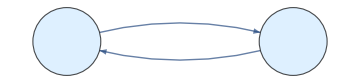

siphons are{{i_1,i_12},{i_2,i_12}} edges are{1→2,2→1}  DFE is{s→s_0,i_1→0,i_12→0,i_2→0} repr. functions  {(R_1 s)/s_0,(R_2 s)/s_0,(R_3 s)/s_0}

K=((R_1 s)/s_0 | (β_1 s)/μ_3 | 0
0 | (R_3 s)/s_0 | 0
0 | (β_2 s)/μ_3 | (R_2 s)/s_0)F=((μ_1 R_1 s)/s_0 | β_1 s | 0
0 | (μ_3 R_3 s)/s_0 | 0
0 | β_2 s | (μ_2 R_2 s)/s_0)V=(μ_1 | 0 | 0
0 | μ_3 | 0
0 | 0 | μ_2)

Ko.pdf

((R_1 s)/s_0 | 0 | (β_1 s)/μ_3
0 | (R_2 s)/s_0 | (β_2 s)/μ_3
0 | 0 | (R_3 s)/s_0)

((μ_1 R_1 s)/s_0 | 0 | β_1 s
0 | (μ_2 R_2 s)/s_0 | β_2 s
0 | 0 | (μ_3 R_3 s)/s_0)

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];
<<EpidCRN`;
Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
Format[mu1]:=Subscript[μ,1];Format[mu2]:=Subscript[μ,2];Format[mu3]:=Subscript[μ,3];Format[mu0]:=Subscript[μ,0];
Format[R1]:=Subscript[R,1];Format[R2]:=Subscript[R,2];Format[R3]:=Subscript[R,3];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];Format[s0]:=Subscript[s,0];
Format[th]:=θ;
Format[La]:=Λ;
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[i12]:=Subscript[i,12];

cLog={be1->0,be2->0,ga1->0,ga2->0,b->r*s*(1-s/s0),mu0->0};
cbg={be1->0,be2->0,ga1->0,ga2->0};
cbe={be1->0,be2->0};cb=b->s0 mu0;cga={ga1->0,ga2->0};
cet={et1->s13 mu1 mu3 (R1-R3)/((s0-s13)mu0 s0),
et2->s23 mu2 mu3 (R2-R3)/((s0-s23)mu0 s0)};
cmu={mu2 ->mu,mu3->mu,mu1 ->mu,mu0->mu};
c3={i12->0};c2={i2->0};c1={i1->0};cb=b->r*s*(1-s/s0);
(*Two-Strain Coinfection Model with Logistic Growth*)
RN={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"+"i12"->2*"i12","i1"+"i2"->"i2"+"i12","i1"+"i2"->"i1"+"i12","i1"+"i12"->2*"i12","i2"+"i12"->2*"i12","s"+"i12"->"i1"+"i12","s"+"i12"->"i2"+"i12","s"->0,"i1"->0,"i2"->0,"i12"->0};
rts={s0 mu0,mu1 s0^(-1)  *R1*s*i1,mu2  s0^(-1)  *R2*s*i2,mu3  s0^(-1)  *R3*s*i12,ga1*i1*i2,ga2*i1*i2,et1*i1*i12,et2*i2*i12,be1*s*i12,be2*s*i12,mu0*s,mu1*i1,mu2*i2,mu3*i12};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,gam,ng}= bdAn[RN,rts];
{edg,cyc,graph}=IGMS[RN, mSi];
Print["siphons are",mSi," edges are",edg,"  DFE is",E0," repr. functions  ",R0A];F=ng[[2]];V=ng[[3]];
Print["K=",K//MatrixForm,"F=",F//MatrixForm,"V=",V//MatrixForm];

Export["Ko.pdf",graph]
per={1,3,2};K[[per,per]]//MatrixForm
F[[per,per]]//MatrixForm
```

reactions and transitions: (0→s | μ_0 s_0
i1+s→2 i1 | (i_1 μ_1 R_1 s)/s_0
i2+s→2 i2 | (i_2 μ_2 R_2 s)/s_0
i12+s→2 i12 | (i_12 μ_3 R_3 s)/s_0
i1+i12→2 i12 | η_1 i_1 i_12
i12+i2→2 i12 | η_2 i_12 i_2
s→0 | μ_0 s
i1→0 | i_1 μ_1
i2→0 | i_2 μ_2
i12→0 | i_12 μ_3)

RHS=(k1-(i_1 k2+i_2 k3+i_12 k4+k7) s
-i_1 (i_12 k5+k8-k2 s)
-i_2 (i_12 k6+k9-k3 s)
i_12 (-k10+i_1 k5+i_2 k6+k4 s))mSi={{i_1},{i_2},{i_12}}

Minimal siphons: {T_1={i_1},T_2={i_2},T_3={i_12}}

IGMS edges: {1→3,2→3,3→1,3→2}

Cycles in IGMS (2 found):

Cycle 1: {2->3,3->2}

Cycle 2: {1->3,3->1}

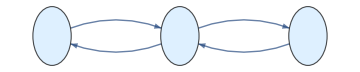

siphons are{{i_1},{i_2},{i_12}} edges are{1→3,2→3,3→1,3→2}  DFE is{s→s_0,i_1→0,i_12→0,i_2→0} repr. functions  {(R_1 s)/s_0,(R_2 s)/s_0,(R_3 s)/s_0}

K=((R_1 s)/s_0 | 0 | 0
0 | (R_3 s)/s_0 | 0
0 | 0 | (R_2 s)/s_0)F=((μ_1 R_1 s)/s_0 | 0 | 0
0 | (μ_3 R_3 s)/s_0 | 0
0 | 0 | (μ_2 R_2 s)/s_0)V=(μ_1 | 0 | 0
0 | μ_3 | 0
0 | 0 | μ_2)

```mathematica
(*part. case*)RNbg={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"+"i12"->2*"i12","i1"+"i12"->2*"i12","i2"+"i12"->2*"i12","s"->0,"i1"->0,"i2"->0,"i12"->0};

rtsbg={s0 mu0,mu1 s0^(-1)  *R1*s*i1,mu2  s0^(-1)  *R2*s*i2,mu3  s0^(-1)  *R3*s*i12,et1*i1*i12,et2*i2*i12,mu0*s,mu1*i1,mu2*i2,mu3*i12};
Print["reactions and transitions: ",Transpose[{RNbg,rtsbg}]//MatrixForm]
{spe, al, be, gamma, Rv, RHS,mSi, {defFormula, defTerms, defResult}}=extMat[RNbg];
Print["RHS=",RHS//FullSimplify//MatrixForm,"mSi=",mSi];
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,gam,ng}= bdAn[RNbg,rtsbg];
{edg,cyc,graph}=IGMS[RN, mSi];
Print["siphons are",mSi," edges are",edg,"  DFE is",E0," repr. functions  ",R0A];F=ng[[2]];V=ng[[3]];
Print["K=",K//MatrixForm,"F=",F//MatrixForm,"V=",V//MatrixForm];
```

```mathematica
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infV,gam,Et}=bdCo[RNbg, rtsbg];
Print["The ", Et//Length ," Et elts have  3,3,2 coms "];
Print["Et1= ",Et1=Et[[1]],"Et2= ",
Et2=Et[[2]],"Et3= ",
Et3=Et[[3]]];
eq=Thread[(RHS/.cbg/.c2)==0];
so=Solve[eq,var]//FullSimplify;(*4 solutions*)
Print["the",so//Length,"sols on siphon 2 are",so];
jac=Grad[RHS,var];
```

The 3 Et elts have  3,3,2 coms

Et1= {{i_12→0,i_2→(μ_0 (-1+R_2) s_0)/(μ_2 R_2),s→s_0/R_2,i_1→0},{i_12→(μ_0 (-1+R_3) s_0)/(μ_3 R_3),i_2→0,s→s_0/R_3,i_1→0},{i_12→-(μ_2 (μ_2 μ_3 R_2-μ_2 μ_3 R_3+η_2 μ_0 s_0-η_2 μ_0 R_2 s_0))/(η_2 (μ_2 μ_3 R_2-μ_2 μ_3 R_3+η_2 μ_0 s_0)),i_2→(μ_2 μ_3^2 R_2-μ_2 μ_3^2 R_3+η_2 μ_0 μ_3 s_0-η_2 μ_0 μ_3 R_3 s_0)/(η_2 (μ_2 μ_3 R_2-μ_2 μ_3 R_3+η_2 μ_0 s_0)),s→(η_2 μ_0 s_0^2)/(μ_2 μ_3 R_2-μ_2 μ_3 R_3+η_2 μ_0 s_0),i_1→0}}Et2= {{i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_12→0,s→s_0/R_1,i_2→0},{i_1→0,i_12→(μ_0 (-1+R_3) s_0)/(μ_3 R_3),s→s_0/R_3,i_2→0},{i_1→(μ_1 μ_3^2 R_1-μ_1 μ_3^2 R_3+η_1 μ_0 μ_3 s_0-η_1 μ_0 μ_3 R_3 s_0)/(η_1 (μ_1 μ_3 R_1-μ_1 μ_3 R_3+η_1 μ_0 s_0)),i_12→-(μ_1 (μ_1 μ_3 R_1-μ_1 μ_3 R_3+η_1 μ_0 s_0-η_1 μ_0 R_1 s_0))/(η_1 (μ_1 μ_3 R_1-μ_1 μ_3 R_3+η_1 μ_0 s_0)),s→(η_1 μ_0 s_0^2)/(μ_1 μ_3 R_1-μ_1 μ_3 R_3+η_1 μ_0 s_0),i_2→0}}Et3= {{i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_2→0,s→s_0/R_1,i_12→0},{i_1→0,i_2→(μ_0 (-1+R_2) s_0)/(μ_2 R_2),s→s_0/R_2,i_12→0}}

Solve::svars: Equations may not give solutions for all "solve" variables.

the4sols on siphon 2 are{{s→s_0,i_1→0,i_12→0},{s→s_0/R_1,i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_12→0},{s→s_0/R_3,i_1→0,i_12→(μ_0 (-1+R_3) s_0)/(μ_3 R_3)},{s→(η_1 μ_0 s_0^2)/(μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0),i_1→(μ_3 (μ_1 μ_3 (R_1-R_3)-η_1 μ_0 (-1+R_3) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0)),i_12→(μ_1 (μ_1 μ_3 (-R_1+R_3)+η_1 μ_0 (-1+R_1) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0))}}

```mathematica
(*all fps*)
eq=Thread[RHS==0];so=Solve[eq,var];(*7 solutions*)
Print[so//Length," sols"]
so//FullSimplify
cD=so[[1]];cE1=so[[2]];cE2=so[[3]];cE3=so[[5]];cEE=so[[4]];c13=so[[6]];
Print["s13= ",s13=s/.c13//FullSimplify]
i131=i1/.c13; i131-mu3(1-R3 s13/s0) /et1//FullSimplify
i133=i12/.c13//FullSimplify;
i133-(R1 s13/s0 -1)mu1/et1//FullSimplify
c23=so[[7]];
con=Join[cp,Thread[Drop[var/.cE1,{3,4}]>0]];
jEE=jac/.cEE//FullSimplify;
(*Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[jEE,u]]]//Factor*)
EE=var/.cEE;
ine=Join[Thread[EE>0],cp,{et1 mu2>et2 mu1,R2<R1<R2 et1 mu2/et2 mu1}]
ret=Reduce[ine/.cmu];re=FullSimplify[ret,cp]
(*{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
ll//Length
ql//Length
hDeg*)

(*con=Join[cp,Thread[Drop[var/.c13,3]>0]];
Print["E13 exists if"]
re11=reCL[Reduce[con]//Factor]*)
```

7 sols

{{s→s_0,i_1→0,i_2→0,i_12→0},{s→s_0/R_1,i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_2→0,i_12→0},{s→s_0/R_2,i_1→0,i_2→(μ_0 (-1+R_2) s_0)/(μ_2 R_2),i_12→0},{s→((η_2 μ_1-η_1 μ_2) s_0)/(η_2 μ_1 R_1-η_1 μ_2 R_2),i_1→(μ_2 (-η_2 μ_1+η_1 μ_2) μ_3 (R_2-R_3)+η_2 μ_0 (η_2 μ_1 (-1+R_1)-η_1 μ_2 (-1+R_2)) s_0)/((η_2 μ_1-η_1 μ_2) (η_2 μ_1 R_1-η_1 μ_2 R_2)),i_2→(μ_1 (η_2 μ_1-η_1 μ_2) μ_3 (R_1-R_3)+η_1 μ_0 (η_2 (μ_1-μ_1 R_1)+η_1 μ_2 (-1+R_2)) s_0)/((η_2 μ_1-η_1 μ_2) (η_2 μ_1 R_1-η_1 μ_2 R_2)),i_12→(μ_1 μ_2 (-R_1+R_2))/(η_2 μ_1 R_1-η_1 μ_2 R_2)},{s→s_0/R_3,i_1→0,i_2→0,i_12→(μ_0 (-1+R_3) s_0)/(μ_3 R_3)},{s→(η_1 μ_0 s_0^2)/(μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0),i_1→(μ_3 (μ_1 μ_3 (R_1-R_3)-η_1 μ_0 (-1+R_3) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0)),i_2→0,i_12→(μ_1 (μ_1 μ_3 (-R_1+R_3)+η_1 μ_0 (-1+R_1) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0))},{s→(η_2 μ_0 s_0^2)/(μ_2 μ_3 (R_2-R_3)+η_2 μ_0 s_0),i_1→0,i_2→(μ_3 (μ_2 μ_3 (R_2-R_3)-η_2 μ_0 (-1+R_3) s_0))/(η_2 (μ_2 μ_3 (R_2-R_3)+η_2 μ_0 s_0)),i_12→(μ_2 (μ_2 μ_3 (-R_2+R_3)+η_2 μ_0 (-1+R_2) s_0))/(η_2 (μ_2 μ_3 (R_2-R_3)+η_2 μ_0 s_0))}}

s13= (η_1 μ_0 s_0^2)/(μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0)

0

0

{((η_2 μ_1-η_1 μ_2) s_0)/(η_2 μ_1 R_1-η_1 μ_2 R_2)>0,(-η_2 μ_1 μ_2 μ_3 R_2+η_1 μ_2^2 μ_3 R_2+η_2 μ_1 μ_2 μ_3 R_3-η_1 μ_2^2 μ_3 R_3-η_2^2 μ_0 μ_1 s_0+η_1 η_2 μ_0 μ_2 s_0+η_2^2 μ_0 μ_1 R_1 s_0-η_1 η_2 μ_0 μ_2 R_2 s_0)/((η_2 μ_1-η_1 μ_2) (η_2 μ_1 R_1-η_1 μ_2 R_2))>0,(η_2 μ_1^2 μ_3 R_1-η_1 μ_1 μ_2 μ_3 R_1-η_2 μ_1^2 μ_3 R_3+η_1 μ_1 μ_2 μ_3 R_3+η_1 η_2 μ_0 μ_1 s_0-η_1^2 μ_0 μ_2 s_0-η_1 η_2 μ_0 μ_1 R_1 s_0+η_1^2 μ_0 μ_2 R_2 s_0)/((η_2 μ_1-η_1 μ_2) (η_2 μ_1 R_1-η_1 μ_2 R_2))>0,-(μ_1 μ_2 (R_1-R_2))/(η_2 μ_1 R_1-η_1 μ_2 R_2)>0,η_1>0,η_2>0,μ_0>0,μ_1>0,μ_2>0,μ_3>0,R_1>0,R_2>0,R_3>0,s_0>0,η_1 μ_2>η_2 μ_1,R_2<R_1<(η_1 μ_1 μ_2 R_2)/η_2}

R_2>1&&R_1>R_2&&η_1>(η_2 (-1+R_1))/(-1+R_2)&&R_3<(-η_2 R_1+η_1 R_2)/(η_1-η_2)&&μ>√((η_2 R_1)/(η_1 R_2))&&((η_1-η_2) μ (R_1-R_3))/(η_1 (η_2-η_2 R_1+η_1 (-1+R_2)))<s_0<-((η_1-η_2) μ (R_2-R_3))/(η_2 (η_1+η_2 (-1+R_1)-η_1 R_2))

```mathematica
re
```

R_1>1&&R_3<(η_2 μ_1 R_1-η_1 μ_2 R_2)/(η_2 μ_1-η_1 μ_2)&&(μ_1 (-η_2 μ_1+η_1 μ_2) μ_3 (R_1-R_3))/(η_1 (η_2 (μ_1-μ_1 R_1)+η_1 μ_2 (-1+R_2)) s_0)<μ_0<(μ_2 (η_2 μ_1-η_1 μ_2) μ_3 (R_2-R_3))/(η_2 (η_2 μ_1 (-1+R_1)-η_1 μ_2 (-1+R_2)) s_0)&&((R_2>1&&(μ_1≥1||R_2≤R_1/(-μ_1^2 (-1+R_1)+R_1))&&(μ_1<1||R_2<R_1)&&η_1>(η_2 μ_1 (-1+R_1))/(μ_2 (-1+R_2)))||(η_1 μ_1 μ_2 R_2>η_2 R_1&&R_1/(-μ_1^2 (-1+R_1)+R_1)<R_2<R_1&&μ_1<1))

```mathematica
(*Stab E1*)
j1=jac/.cE1//FullSimplify;j1//MatrixForm
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
```

```mathematica
lSta
qSta
Print["E1 stable if R1(s13) >1"]
re=reCL[Reduce[Join[cp,lSta,qSta]]//FullSimplify]//FullSimplify
cpL=And@@Drop[cp,-1]&&R1>1;
re1=FullSimplify[re,cpL]
```

{μ_2 R_1-μ_2 R_2>0,μ_1 μ_3 R_1-μ_1 μ_3 R_3+μ_0 s_0 η_1-μ_0 R_1 s_0 η_1>0}

{μ_0 R_1>0,-μ_0 μ_1+μ_0 μ_1 R_1>0}

E1 stable if R1(s13) >1

(R_1>R_3&&R_3>1&&μ_0<(μ_1 μ_3 (R_1-R_3))/((-1+R_1) s_0 η_1)&&R_2<R_1)||(R_1>1&&R_1>R_2&&μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_1) s_0 η_1<0&&R_3≤1)

μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_1) s_0 η_1<0&&R_1>R_2&&(R_1>R_3||R_3≤1)

```mathematica
(*Stab E3*)j3=jac/.cE3//FullSimplify;j3//MatrixForm
Print[" At cE3, chp of jac, ch3, factorizes as"]
ch3=Numerator[Together[CharacteristicPolynomial[j3,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch3,par];
ll//Length
ql//Length
hDeg

ret=Reduce[Join[cp,lSta,qSta,{R3>1(*,R1>R2*)}]]//FullSimplify;
cond=And@@cp&&R3>1
Print["E3 stable if R1(s11) <1"]
re3=FullSimplify[ret,cond]
re3//Length
re31=re3[[1]]
re31//Length
re32=re3[[2]];re=BooleanMinimize[LogicalExpand[re3]]//FullSimplify
FullSimplify[re3,cond]
FullSimplify[re,cond]
lo=LogicalExpand[re]
Resolve[lo,Reals]
```

(-μ_0 R_3 | -(μ_1 R_1)/R_3 | -(μ_2 R_2)/R_3 | -μ_3
0 | (μ_1 μ_3 (R_1-R_3)-μ_0 (-1+R_3) s_0 η_1)/(μ_3 R_3) | 0 | 0
0 | 0 | (μ_2 μ_3 (R_2-R_3)-μ_0 (-1+R_3) s_0 η_2)/(μ_3 R_3) | 0
μ_0 (-1+R_3) | (μ_0 (-1+R_3) s_0 η_1)/(μ_3 R_3) | (μ_0 (-1+R_3) s_0 η_2)/(μ_3 R_3) | 0)

At cE3, chp of jac, ch3, factorizes as

(-μ_0 μ_3+μ_0 μ_3 R_3+μ_0 R_3 u+u^2) (-μ_1 μ_3 R_1+μ_1 μ_3 R_3+μ_3 R_3 u-μ_0 s_0 η_1+μ_0 R_3 s_0 η_1) (-μ_2 μ_3 R_2+μ_2 μ_3 R_3+μ_3 R_3 u-μ_0 s_0 η_2+μ_0 R_3 s_0 η_2)

2

1

{}

μ_0>0&&μ_1>0&&μ_2>0&&μ_3>0&&R_1>0&&R_2>0&&R_3>0&&s_0>0&&η_1>0&&η_2>0&&R_3>1

E3 stable if R1(s11) <1

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

2

R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0

2

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤1)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤R_3)||(μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0&&R_1≤R_3)||(R_1≤R_3&&R_2≤1)||(R_1≤R_3&&R_2≤R_3)

(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤1)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤R_3)||(μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0&&R_1≤R_3)||(R_1≤R_3&&R_2≤1)||(R_1≤R_3&&R_2≤R_3)

```mathematica
(*Stab E13*)
j13=jac/.c13//FullSimplify;
Print[" At cE13, chp of jac factorizes as"]
ch13=Numerator[Together[CharacteristicPolynomial[j13,u]]]//Factor
ch13//Length
co2=CoefficientList[ch13[[2]],u]//FullSimplify
```

At cE13, chp of jac factorizes as

(μ_1^4 μ_3^4 R_1^3-3 μ_1^4 μ_3^4 R_1^2 R_3+3 μ_1^4 μ_3^4 R_1 R_3^2-μ_1^4 μ_3^4 R_3^3-μ_1^3 μ_3^3 R_1^3 u^2+3 μ_1^3 μ_3^3 R_1^2 R_3 u^2-3 μ_1^3 μ_3^3 R_1 R_3^2 u^2+μ_1^3 μ_3^3 R_3^3 u^2+3 μ_0 μ_1^3 μ_3^3 R_1^2 s_0 η_1-μ_0 μ_1^3 μ_3^3 R_1^3 s_0 η_1-6 μ_0 μ_1^3 μ_3^3 R_1 R_3 s_0 η_1+μ_0 μ_1^3 μ_3^3 R_1^2 R_3 s_0 η_1+3 μ_0 μ_1^3 μ_3^3 R_3^2 s_0 η_1+μ_0 μ_1^3 μ_3^3 R_1 R_3^2 s_0 η_1-μ_0 μ_1^3 μ_3^3 R_3^3 s_0 η_1+μ_1^3 μ_3^3 R_1^2 s_0 u η_1-μ_0 μ_1^3 μ_3^2 R_1^3 s_0 u η_1-2 μ_1^3 μ_3^3 R_1 R_3 s_0 u η_1+μ_0 μ_1^3 μ_3^2 R_1^2 R_3 s_0 u η_1+μ_1^3 μ_3^3 R_3^2 s_0 u η_1+μ_0 μ_1^2 μ_3^3 R_1 R_3^2 s_0 u η_1-μ_0 μ_1^2 μ_3^3 R_3^3 s_0 u η_1-3 μ_0 μ_1^2 μ_3^2 R_1^2 s_0 u^2 η_1+6 μ_0 μ_1^2 μ_3^2 R_1 R_3 s_0 u^2 η_1-3 μ_0 μ_1^2 μ_3^2 R_3^2 s_0 u^2 η_1-μ_1^2 μ_3^2 R_1^2 s_0 u^3 η_1+2 μ_1^2 μ_3^2 R_1 R_3 s_0 u^3 η_1-μ_1^2 μ_3^2 R_3^2 s_0 u^3 η_1+3 μ_0^2 μ_1^2 μ_3^2 R_1 s_0^2 η_1^2-2 μ_0^2 μ_1^2 μ_3^2 R_1^2 s_0^2 η_1^2-3 μ_0^2 μ_1^2 μ_3^2 R_3 s_0^2 η_1^2+μ_0^2 μ_1^2 μ_3^2 R_1^2 R_3 s_0^2 η_1^2+2 μ_0^2 μ_1^2 μ_3^2 R_3^2 s_0^2 η_1^2-μ_0^2 μ_1^2 μ_3^2 R_1 R_3^2 s_0^2 η_1^2+2 μ_0 μ_1^2 μ_3^2 R_1 s_0^2 u η_1^2-μ_0^2 μ_1^2 μ_3 R_1^2 s_0^2 u η_1^2-μ_0 μ_1^2 μ_3^2 R_1^2 s_0^2 u η_1^2-2 μ_0 μ_1^2 μ_3^2 R_3 s_0^2 u η_1^2+μ_0^2 μ_1^2 μ_3 R_1^2 R_3 s_0^2 u η_1^2+μ_0^2 μ_1 μ_3^2 R_3^2 s_0^2 u η_1^2+μ_0 μ_1^2 μ_3^2 R_3^2 s_0^2 u η_1^2-μ_0^2 μ_1 μ_3^2 R_1 R_3^2 s_0^2 u η_1^2-3 μ_0^2 μ_1 μ_3 R_1 s_0^2 u^2 η_1^2+3 μ_0^2 μ_1 μ_3 R_3 s_0^2 u^2 η_1^2-2 μ_0 μ_1 μ_3 R_1 s_0^2 u^3 η_1^2+2 μ_0 μ_1 μ_3 R_3 s_0^2 u^3 η_1^2+μ_0^3 μ_1 μ_3 s_0^3 η_1^3-μ_0^3 μ_1 μ_3 R_1 s_0^3 η_1^3-μ_0^3 μ_1 μ_3 R_3 s_0^3 η_1^3+μ_0^3 μ_1 μ_3 R_1 R_3 s_0^3 η_1^3+μ_0^2 μ_1 μ_3 s_0^3 u η_1^3-μ_0^2 μ_1 μ_3 R_1 s_0^3 u η_1^3-μ_0^2 μ_1 μ_3 R_3 s_0^3 u η_1^3+μ_0^2 μ_1 μ_3 R_1 R_3 s_0^3 u η_1^3-μ_0^3 s_0^3 u^2 η_1^3-μ_0^2 s_0^3 u^3 η_1^3) (-μ_1 μ_2 μ_3 R_1 η_1+μ_1 μ_2 μ_3 R_3 η_1-μ_1 μ_3 R_1 u η_1+μ_1 μ_3 R_3 u η_1-μ_0 μ_2 s_0 η_1^2+μ_0 μ_2 R_2 s_0 η_1^2-μ_0 s_0 u η_1^2+μ_1^2 μ_3 R_1 η_2-μ_1^2 μ_3 R_3 η_2+μ_0 μ_1 s_0 η_1 η_2-μ_0 μ_1 R_1 s_0 η_1 η_2)

2

{μ_0 μ_2 (-1+R_2) s_0 η_1^2+μ_1^2 μ_3 (R_1-R_3) η_2+μ_1 η_1 (μ_2 μ_3 (-R_1+R_3)-μ_0 (-1+R_1) s_0 η_2),-η_1 (μ_1 μ_3 (R_1-R_3)+μ_0 s_0 η_1)}

```mathematica
v23=Drop[var/.c23//FullSimplify,{2}];
(*Print["E23 exists if"]*)
re2=reCL[Factor/@Reduce[Join[cp,Thread[v23>0]]]];
Print["EE exists if"]
reE=reCL[Factor/@Reduce[Join[cp,Thread[(var/.cEE)>0],{R1>R2}]]]
reE[[2,1]]
```

EE exists if

R_2>1&&R_1>R_2&&0<μ_1<(μ_2 (-1+R_2) η_1)/((-1+R_1) η_2)&&0<R_3<(μ_2 R_2 η_1-μ_1 R_1 η_2)/(μ_2 η_1-μ_1 η_2)&&(μ_1 μ_3 (R_1-R_3) (-μ_2 η_1+μ_1 η_2))/(s_0 η_1 (μ_2 η_1-μ_2 R_2 η_1-μ_1 η_2+μ_1 R_1 η_2))<μ_0<(μ_2 μ_3 (R_2-R_3) (μ_2 η_1-μ_1 η_2))/(s_0 η_2 (-μ_2 η_1+μ_2 R_2 η_1+μ_1 η_2-μ_1 R_1 η_2))

```mathematica
cpl=And@@cp;
fi=FindInstance[reE&&re1&&re2&&cpl&&R1>1&&R2>1&&R3>1,par]
```

{{μ_0→5/4,μ_1→3/2,μ_2→1,μ_3→1,R_1→39/32,R_2→5/4,R_3→17/16,s_0→1,η_1→1,η_2→1}}

```mathematica
Timing[re=reCL[Reduce[reE&&re1&&re2&&cpl&&R1>1&&R2>1&&R3>1]//FullSimplify]]
```

$Aborted

```mathematica
(*DSR[RN]:construct Directed Signed Species-Reaction (DSR) graph from RN*)ClearAll[DSR];
DSR[RN_List]:=Module[{reactions,nR,rnodes,snodes,vertices,edges,edgeLabels,DSRGraph,DSRresult},(*Use parseComplex (already defined in EpidCRN for IGMS)*)(*Assumes parseComplex[complex] returns association <|species->stoich|>*)(*Get species using existing extSpe*)snodes=extSpe[RN];
(*canonical reactions:{index,reactComp,prodComp} as associations*)reactions=Table[{i,parseComplex[RN[[i,1]]],parseComplex[RN[[i,2]]]},{i,Length[RN]}];
nR=Length[reactions];
(*reaction node names "R1","R2",...*)rnodes=Table["R"<>ToString[i],{i,nR}];
vertices=Join[snodes,rnodes];
(*build directed edges with sign (+1 product,-1 reactant) and multiplicity label*)edges=Reap[Do[Module[{rComp=reactions[[i,2]],pComp=reactions[[i,3]],rn=rnodes[[i]]},(*reactant arcs:species->reaction,sign=-1*)Do[Sow[{s->rn,-1,rComp[s]}],{s,Keys[rComp]}];
(*product arcs:reaction->species,sign=+1*)Do[Sow[{rn->p,+1,pComp[p]}],{p,Keys[pComp]}];],{i,nR}]][[2,1]];
(*normalize edges->list of associations*)edgeLabels=edges/. {x_->y_,s_,m_}:><|"edge"->(x->y),"sign"->s,"stoich"->m|>;
(*Graph construction*)DSRGraph=Graph[vertices,(#["edge"]&)/@edgeLabels,VertexLabels->Placed[Automatic,Center],EdgeLabels->Thread[(#["edge"]&/@edgeLabels)->((#["sign"]/. {1->"+",-1->"-"})<>ToString[#["stoich"]]&/@edgeLabels)],VertexShapeFunction->(If[StringMatchQ[ToString[#2],"R"~~__],"Square","Circle"]&),ImagePadding->10,GraphLayout->"LayeredDigraphEmbedding",DirectedEdges->True];
DSRresult=<|"Graph"->DSRGraph,"EdgeData"->edgeLabels,"ReactionNodes"->rnodes,"SpeciesNodes"->snodes|>;
DSRresult];

DSR::usage="DSR[RN] constructs a Directed Signed Species-Reaction (DSR) graph. Returns an association with Graph, EdgeData (sign and stoichiometry), ReactionNodes, and SpeciesNodes.";

(*----Test parseComplex----*)
Print["=== Testing parseComplex ==="];
Print["parseComplex[0] = ",parseComplex[0]];
Print["parseComplex[\"A\"] = ",parseComplex["A"]];
Print["parseComplex[\"A\" + \"B\"] = ",parseComplex["A"+"B"]];
Print["parseComplex[2*\"C\"] = ",parseComplex[2*"C"]];
Print["parseComplex[\"A\" + 2*\"B\" + 3*\"C\"] = ",parseComplex["A"+2*"B"+3*"C"]];
```

=== Testing parseComplex ===

parseComplex[0] = <||>

parseComplex["A"] = <|A→1|>

parseComplex["A" + "B"] = <|A→1,B→1|>

parseComplex[2*"C"] = <|C→2|>

parseComplex["A" + 2*"B" + 3*"C"] = <|A→1,B→2,C→3|>

```mathematica
(* ====DSR:Directed Species-Reaction Graph====*)DSR::usage="DSR[RN] builds the directed species-reaction (SR) bipartite graph for reaction network RN.
Returns an association with keys:
  \"Graph\" -> the Graph object with signed, stoichiometric edge labels
  \"EdgeData\" -> list of associations {<|\"edge\"->_, \"sign\"->_, \"stoich\"->_|>, ...}
  \"ReactionNodes\" -> list of reaction node labels {\"R1\", \"R2\", ...}
  \"SpeciesNodes\" -> list of species node labels";

DSR[RN_List]:=Module[{snodes,rnodes,vertices,edges,edgeLabels,parsedRN,rComp,pComp,rSpecies,pSpecies,DSRGraph,DSRresult},(*Species nodes*)snodes=extSpe[RN];
(*Reaction nodes*)rnodes=Table["R"<>ToString[i],{i,Length[RN]}];
(*All vertices*)vertices=Join[snodes,rnodes];
(*Parse each reaction*)parsedRN=Table[rComp=parseComplex[RN[[i,1]]];
pComp=parseComplex[RN[[i,2]]];
rSpecies=Keys[rComp];
pSpecies=Keys[pComp];
{i,rComp,pComp,rSpecies,pSpecies},{i,Length[RN]}];
(*Build edges and labels*)edges={};
edgeLabels={};
Do[With[{rxnNode=rnodes[[i]],rComp=parsedRN[[i,2]],pComp=parsedRN[[i,3]],rSpecies=parsedRN[[i,4]],pSpecies=parsedRN[[i,5]]},(*Reactant->Reaction edges (sign=-1)*)Do[AppendTo[edges,s->rxnNode];
AppendTo[edgeLabels,<|"edge"->(s->rxnNode),"sign"->-1,"stoich"->rComp[s]|>],{s,rSpecies}];
(*Reaction->Product edges (sign=+1)*)Do[AppendTo[edges,rxnNode->s];
AppendTo[edgeLabels,<|"edge"->(rxnNode->s),"sign"->1,"stoich"->pComp[s]|>],{s,pSpecies}];],{i,Length[RN]}];
(*Convert edge labels to rules for EdgeLabels option*)edgeLabelRules=Thread[(#["edge"]&/@edgeLabels)->((#["sign"]/. {1->"+",-1->"-"})<>ToString[#["stoich"]]&/@edgeLabels)];
(*Graph construction*)DSRGraph=Graph[vertices,edges,VertexLabels->Placed[Automatic,Center],EdgeLabels->edgeLabelRules,VertexShapeFunction->(If[StringMatchQ[ToString[#2],"R"~~__],"Square","Circle"]&),ImagePadding->10,GraphLayout->"LayeredDigraphEmbedding",DirectedEdges->True];
DSRresult=<|"Graph"->DSRGraph,"EdgeData"->edgeLabels,"ReactionNodes"->rnodes,"SpeciesNodes"->snodes|>;
DSRresult];

(*----Test parseComplex----*)
Print["=== Testing parseComplex ==="];
Print["parseComplex[0] = ",parseComplex[0]];
Print["parseComplex[\"A\"] = ",parseComplex["A"]];
Print["parseComplex[\"A\" + \"B\"] = ",parseComplex["A"+"B"]];
Print["parseComplex[2*\"C\"] = ",parseComplex[2*"C"]];
Print["parseComplex[\"A\" + 2*\"B\" + 3*\"C\"] = ",parseComplex["A"+2*"B"+3*"C"]];
Print[];

(*----test DSR example----*)
Print["=== Testing DSR ==="];
(*small RN where RN must be a list of rules {lhs->rhs}*)
RN={"A"+"B"->"C",2*"C"->"A"+"B",0->"A"};

DSRresult=DSR[RN];
DSRGraph=DSRresult["Graph"];
Print["Species nodes: ",DSRresult["SpeciesNodes"]];
Print["Reaction nodes: ",DSRresult["ReactionNodes"]];
Print["Edge data: "];
Print[DSRresult["EdgeData"]];

(*----Visualization----*)
Print["\n=== Visualizing DSR Graph ==="];

(*Basic visualization*)
Print["Basic view:"];
DSRGraph

(*Enhanced bipartite layout visualization-FIXED for v13.3*)
Print["\nBipartite layout view:"];

(*Manual bipartite layout for Mathematica 13.3*)
Module[{species,reactions,nSpecies,nReactions,vertexCoords},species=DSRresult["SpeciesNodes"];
reactions=DSRresult["ReactionNodes"];
nSpecies=Length[species];
nReactions=Length[reactions];
(*Place species on left column (x=0),reactions on right column (x=2)*)vertexCoords=Join[Thread[species->Table[{0,i},{i,nSpecies,1,-1}]],Thread[reactions->Table[{2,i},{i,nReactions,1,-1}]]];
Graph[VertexList[DSRGraph],EdgeList[DSRGraph],VertexCoordinates->vertexCoords,VertexLabels->Placed[Automatic,Center],VertexSize->Medium,VertexStyle->{Thread[species->LightBlue],Thread[reactions->LightGreen]},VertexShapeFunction->{Thread[species->"Circle"],Thread[reactions->"Square"]},EdgeLabels->Thread[(#["edge"]&/@DSRresult["EdgeData"])->((#["sign"]/. {1->"+",-1->"-"})<>ToString[#["stoich"]]&/@DSRresult["EdgeData"])],ImageSize->Large,ImagePadding->20]]
```

=== Testing parseComplex ===

parseComplex[0] = <||>

parseComplex["A"] = <|A→1|>

parseComplex["A" + "B"] = <|A→1,B→1|>

parseComplex[2*"C"] = <|C→2|>

parseComplex["A" + 2*"B" + 3*"C"] = <|A→1,B→2,C→3|>

=== Testing DSR ===

Species nodes: {A,B,C}

Reaction nodes: {R1,R2,R3}

Edge data:

{<|edge→A→R1,sign→-1,stoich→1|>,<|edge→B→R1,sign→-1,stoich→1|>,<|edge→R1→C,sign→1,stoich→1|>,<|edge→C→R2,sign→-1,stoich→2|>,<|edge→R2→A,sign→1,stoich→1|>,<|edge→R2→B,sign→1,stoich→1|>,<|edge→R3→A,sign→1,stoich→1|>}

=== Visualizing DSR Graph ===

Basic view:

Bipartite layout view:

```mathematica
Print["║ Test 2: Autocatalytic cycle                                  ║"];
Print["╚═══════════════════════════════════════════════════════════════╝"];
RN2={"A"+"B"->2*"A","A"->"B","B"->0};
res2=testMAS[RN2];


Print["║ Test 3: Three strains with recombination                     ║"];
Print["╚═══════════════════════════════════════════════════════════════╝"];
RN3={"I1"+"S"->2*"I1","I2"+"S"->2*"I2","I12"+"S"->2*"I12","I1"+"I2"->2*"I12",(*recombination*)0->"S","S"->0,"I1"->0,"I2"->0,"I12"->0};
res3=testMAS[RN3];
```

╔═══════════════════════════════════════════════════════════════╗

║ Test 1: Two-strain competition with cross-infection          ║

╚═══════════════════════════════════════════════════════════════╝

═══════════════════════════════════════════════════════════════

MAS Analysis: Minimal Autocatalytic Subnetworks

═══════════════════════════════════════════════════════════════

Network:

R1: I1+R→2 I1
  R2: I2+R→2 I2
  R3: I1+R→I1+I2
  R4: 0→R
  R5: R→0

Warning: Some species not found in network

Species: {I1,R,I2}

Stoichiometric matrix γ (rows=species, cols=reactions):

( | 1 | 2 | 3 | 4 | 5
I1 | 1 | 0 | 0 | 0 | 0
R | -1 | -1 | -1 | 1 | -1
I2 | 0 | 1 | 1 | 0 | 0)

Minimal siphons found: 1

S1: {I1}

MAS (self-replicable minimal siphons): 0

───────────────────────────────────────────────────────────────

Detailed analysis of each minimal siphon:

───────────────────────────────────────────────────────────────

S1: {I1}

MAS? False | Drainable? False | Critical? True

Type: ○ NEUTRAL (neither MAS nor drainable)

Interpretation: Stable

Reason not MAS: species not in network

═══════════════════════════════════════════════════════════════

SUMMARY:

Total minimal siphons: 1

MAS (self-replicable): 0

Critical MAS (→ STRAINS in ME models): 0

═══════════════════════════════════════════════════════════════

╔═══════════════════════════════════════════════════════════════╗

║ Test 2: Autocatalytic cycle                                  ║

╚═══════════════════════════════════════════════════════════════╝

═══════════════════════════════════════════════════════════════

MAS Analysis: Minimal Autocatalytic Subnetworks

═══════════════════════════════════════════════════════════════

Network:

R1: A+B→2 A
  R2: A→B
  R3: B→0

Warning: Some species not found in network

Species: {A,B}

Stoichiometric matrix γ (rows=species, cols=reactions):

( | 1 | 2 | 3
A | 1 | -1 | 0
B | -1 | 1 | -1)

Minimal siphons found: 1

S1: {A}

MAS (self-replicable minimal siphons): 0

───────────────────────────────────────────────────────────────

Detailed analysis of each minimal siphon:

───────────────────────────────────────────────────────────────

S1: {A}

MAS? False | Drainable? False | Critical? True

Type: ○ NEUTRAL (neither MAS nor drainable)

Interpretation: Stable

Reason not MAS: species not in network

═══════════════════════════════════════════════════════════════

SUMMARY:

Total minimal siphons: 1

MAS (self-replicable): 0

Critical MAS (→ STRAINS in ME models): 0

═══════════════════════════════════════════════════════════════

╔═══════════════════════════════════════════════════════════════╗

║ Test 3: Three strains with recombination                     ║

╚═══════════════════════════════════════════════════════════════╝

═══════════════════════════════════════════════════════════════

MAS Analysis: Minimal Autocatalytic Subnetworks

═══════════════════════════════════════════════════════════════

Network:

R1: I1+S→2 I1
  R2: I2+S→2 I2
  R3: I12+S→2 I12
  R4: I1+I2→2 I12
  R5: 0→S
  R6: S→0
  R7: I1→0
  R8: I2→0
  R9: I12→0

Warning: Some species not found in network

Warning: Some species not found in network

Species: {I1,S,I2,I12}

Stoichiometric matrix γ (rows=species, cols=reactions):

( | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
I1 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0
S | -1 | -1 | -1 | 0 | 1 | -1 | 0 | 0 | 0
I2 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1 | 0
I12 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | -1)

Minimal siphons found: 2

S1: {I1}

S2: {I2}

MAS (self-replicable minimal siphons): 0

───────────────────────────────────────────────────────────────

Detailed analysis of each minimal siphon:

───────────────────────────────────────────────────────────────

S1: {I1}

MAS? False | Drainable? False | Critical? True

Type: ○ NEUTRAL (neither MAS nor drainable)

Interpretation: Stable

Reason not MAS: species not in network

S2: {I2}

MAS? False | Drainable? False | Critical? True

Type: ○ NEUTRAL (neither MAS nor drainable)

Interpretation: Stable

Reason not MAS: species not in network

═══════════════════════════════════════════════════════════════

SUMMARY:

Total minimal siphons: 2

MAS (self-replicable): 0

Critical MAS (→ STRAINS in ME models): 0

═══════════════════════════════════════════════════════════════

```mathematica
?EpidCRN`*
```